```mathematica
dataGet[str_String,page_]:=Table[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[i]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,1,page}]
parseData2[dataIn_]:=ToLowerCase@DeleteStopwords@Flatten@TextWords@Table[DeleteCases[Cases[dataRaw,XMLElement["a",_,_],Infinity][[i]],XMLElement["b",_,_],Infinity][[3]],{i,1,Length@dataRaw[[1]]*Length@dataRaw}]
parseData1[dataIn_]:=DeleteStopwords@Flatten@TextWords@Table[Cases[dataIn,XMLElement["a",_,_],Infinity][[i]][[3]][[1]],{i,1,Length@dataRaw[[1]]*Length@dataRaw}]
associate[words_]:=Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];
commonAssociateMinus[dataParsed_,Ncommonest_,minusWords_]:=associate[DeleteCases[Commonest[dataParsed,Ncommonest],minusWords]]
```

```mathematica
(*Get google scholar data from first search page on TI*)
dataRaw=dataGet["thermodynamic integration",1];
```

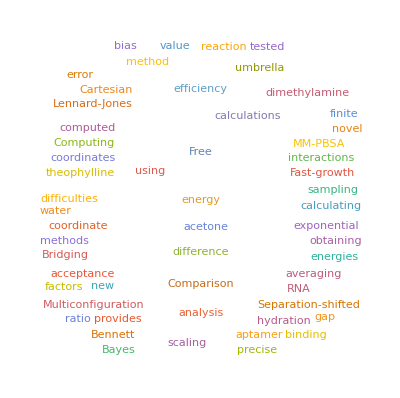

```mathematica
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

```mathematica
(*Get google scholar data from first three search pages on TI*)
dataRaw=dataGet["thermodynamic integration",3];
```

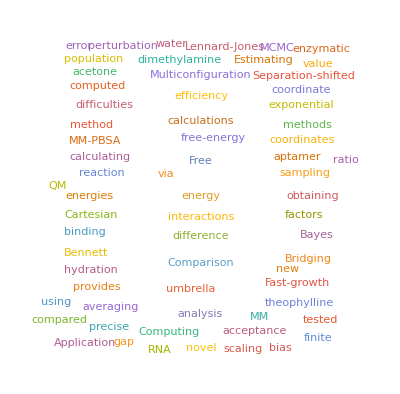

```mathematica
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

```mathematica
(*Get google scholar data from first five search pages on ZrC*)
dataRaw=dataGet["zirconium carbide",5];
```

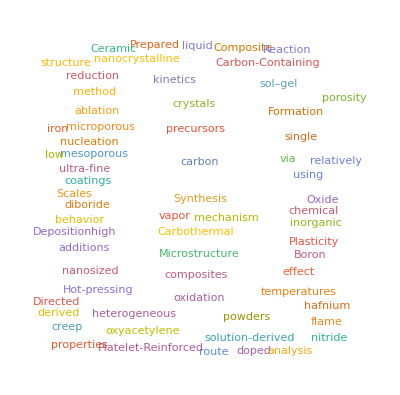

```mathematica
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

```mathematica
(*Get google scholar data from first eight search pages on DFT*)
dataRaw=dataGet["density functional theory",8];
```

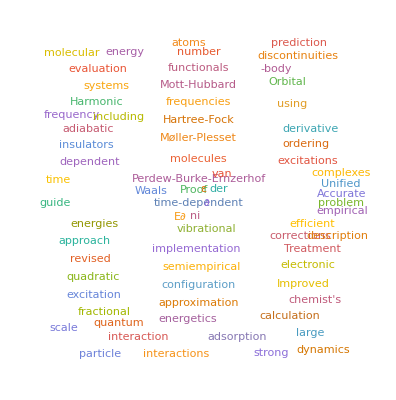

```mathematica
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

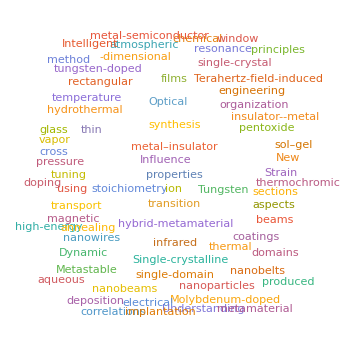

```mathematica
(*Get google scholar data from first 5 search pages on VO2*)
dataRaw=dataGet["vanadium dioxide",5];
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

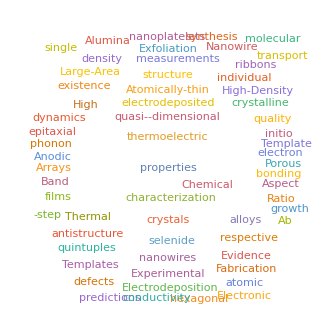

```mathematica
(*Get google scholar data from first 5 search pages on Bi2Te3*)
dataRaw=dataGet["bismuth telluride",5];
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

```mathematica
(*Get google scholar data from first 10 search pages on steganography*)
dataRaw=dataGet["steganography",10];
```

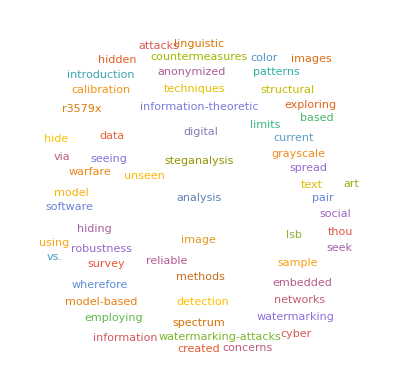

```mathematica
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

```mathematica
(*Get google scholar data from first search page on calphad*)
dataRaw=dataGet["calphad",2];
```

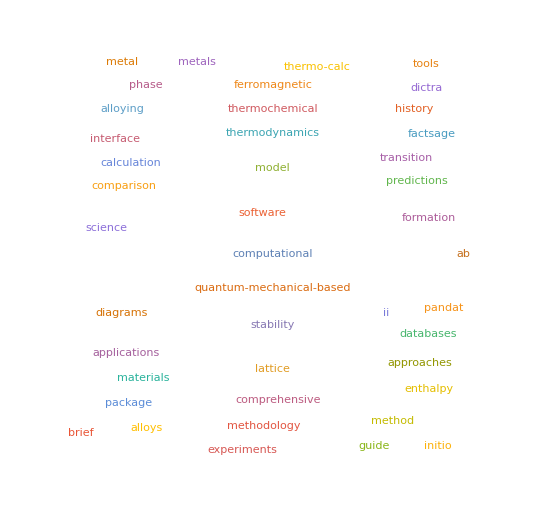

```mathematica
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

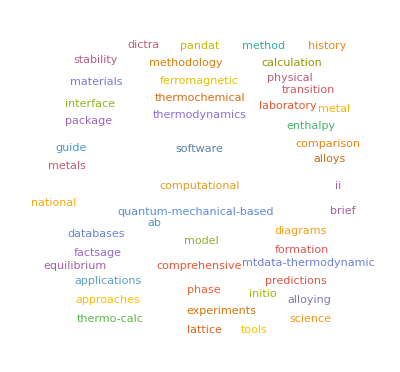

```mathematica
dataParsed=parseData2[dataRaw];
WordCloud@dataParsed
```

```mathematica
dataParsed
```

{ab,initio,lattice,stability,comparison,lattice,stability,thermo-calc,dictra,computational,tools,materials,science,factsage,thermochemical,software,databases,model,alloying,ferromagnetic,metals,computational,thermodynamics,method,brief,history,calculation,phase,diagrams,comprehensive,guide,model,predictions,enthalpy,formation,transition,metal,alloys,ii,pandat,software,package,applications,interface,quantum-mechanical-based,approaches,experiments,methodology,thermo-calc,dictra,computational,tools,materials,science,factsage,thermochemical,software,databases,model,alloying,ferromagnetic,metals,computational,thermodynamics,method,brief,history,calculation,phase,diagrams,comprehensive,guide,model,predictions,enthalpy,formation,transition,metal,alloys,ii,pandat,software,package,applications,interface,quantum-mechanical-based,approaches,experiments,methodology,mtdata-thermodynamic,phase,equilibrium,software,national,physical,laboratory}

```mathematica
associate[words_]:=Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];
```

```mathematica
calphad=DeleteCases[Commonest[dataParsed,20],"ferromagnetic"]
```

{lattice,stability,thermo-calc,dictra,computational,tools,materials,science,factsage,thermochemical,software,databases,model,alloying,metals,thermodynamics,method,brief,phase}

{lattice->science,lattice->factsage,stability->lattice,stability->tools,thermo-calc->thermochemical,thermo-calc->thermodynamics,dictra->factsage,dictra->lattice,computational->materials,computational->lattice,tools->model,tools->metals,materials->metals,materials->lattice,science->lattice,science->brief,factsage->lattice,factsage->dictra,thermochemical->thermo-calc,thermochemical->thermodynamics,software->factsage,software->lattice,databases->lattice,databases->materials,model->tools,model->metals,alloying->lattice,alloying->tools,metals->method,metals->tools,thermodynamics->thermo-calc,thermodynamics->thermochemical,method->metals,method->tools,brief->model,brief->tools,phase->tools,phase->model}

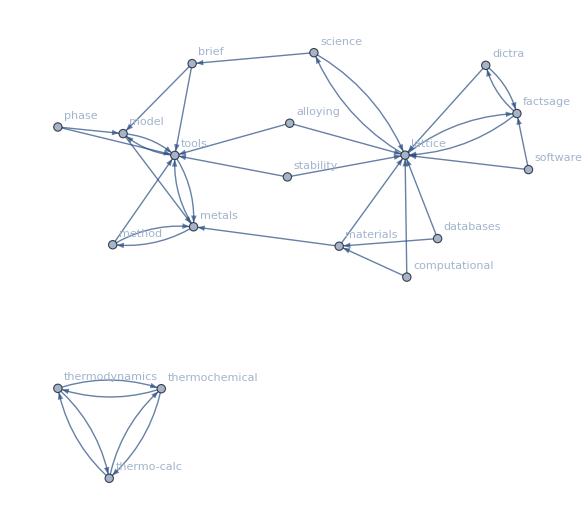

```mathematica
associate[calphad];
Graph[%,VertexLabels->"Name",ImageSize->450]
```

```mathematica
associate[calphad]
```

TreeGraph[{lattice},{lattice->science,lattice->factsage,stability->lattice,stability->tools,thermo-calc->thermochemical,thermo-calc->thermodynamics,dictra->factsage,dictra->lattice,computational->materials,computational->lattice,tools->model,tools->metals,materials->metals,materials->lattice,science->lattice,science->brief,factsage->lattice,factsage->dictra,thermochemical->thermo-calc,thermochemical->thermodynamics,software->factsage,software->lattice,databases->lattice,databases->materials,model->tools,model->metals,alloying->lattice,alloying->tools,metals->method,metals->tools,thermodynamics->thermo-calc,thermodynamics->thermochemical,method->metals,method->tools,brief->model,brief->tools,phase->tools,phase->model}]

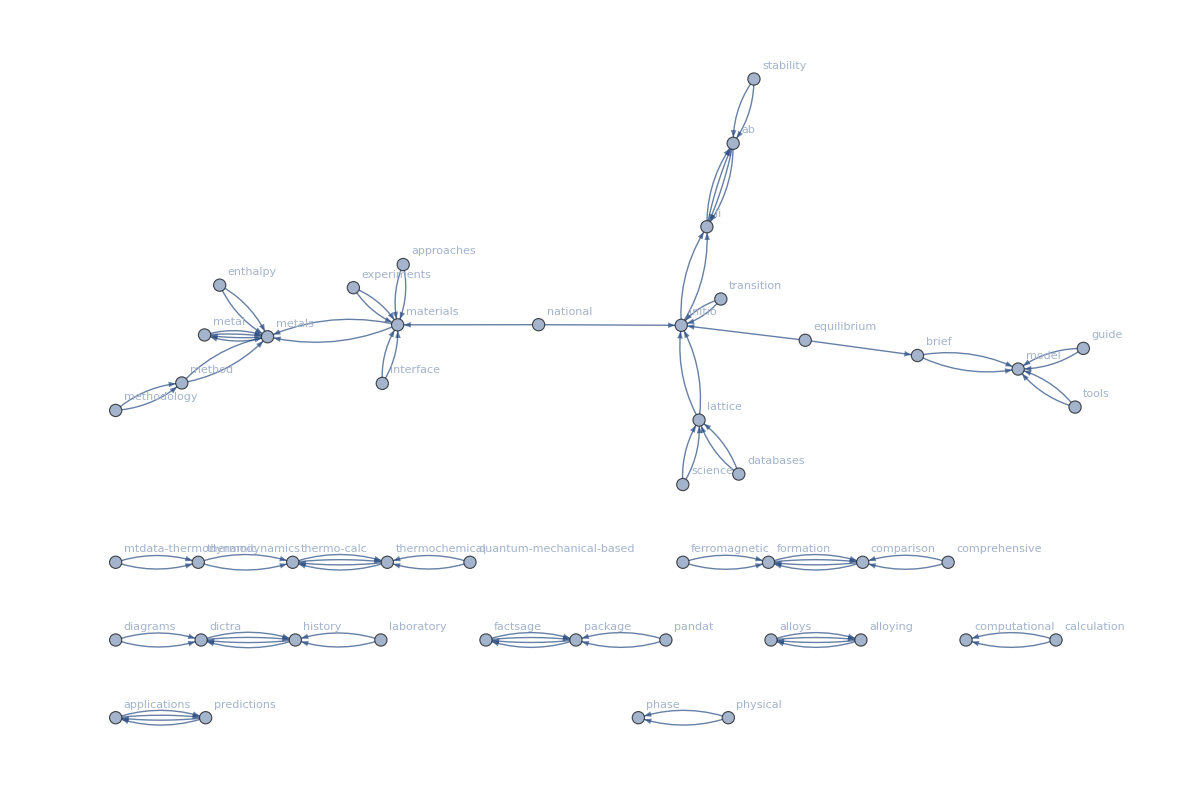

```mathematica
associate[dataParsed];
Graph[%,VertexLabels->"Name",ImageSize->450]
```

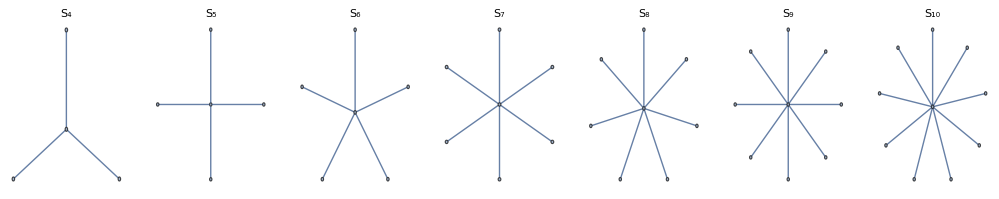

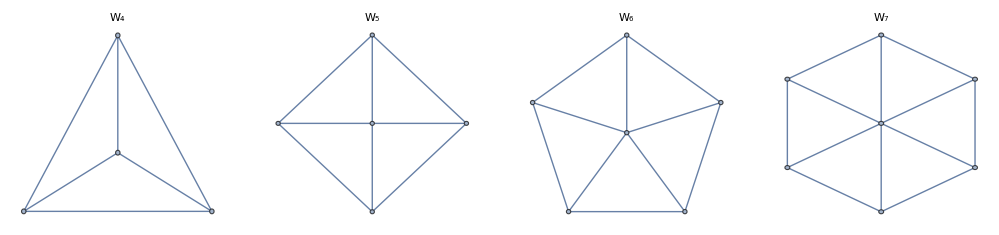

```mathematica
GraphicsGrid@{Table[StarGraph[i,PlotLabel->Subscript[S,i]],{i,4,10}]}
GraphicsGrid@{Table[WheelGraph[i,PlotLabel->Subscript[W,i]],{i,4,7}]}
```

```mathematica
(*Get google scholar data from first search page on tungsten carbide*)
dataRaw=dataGet["tungsten carbide",3];
```

```mathematica
parseData2[dataIn_]:=ToLowerCase@DeleteStopwords@Flatten@TextWords@Table[DeleteCases[Cases[dataRaw,XMLElement["a",_,_],Infinity][[i]],XMLElement["b",_,_],Infinity][[3]],{i,1,((Length@dataRaw[[1]]-1)*Length@dataRaw-1)}]
dataParsed=parseData2[dataRaw]
```

{direct,catalytic,conversion,cellulose,ethylene,glycol,using,nickel-promoted,catalysts,hardness,deformation,cemented,low-cost,molybdenum,counter,electrodes,dye-sensitized,solar,cells,new,catalysts,conversion,methane,synthesis,gas,molybdenum,study,effect,machining,parameters,machining,characteristics,electrical,discharge,machining,synthesis,sintering,mechanical,properties,nanocrystalline,cemented,review,microspheres,noble-metal-economic,electrocatalyst,methanol,oxidation,study,high,velocity,oxy-fuel,thermally,sprayed,based,coatings,1,microstructures,electronic,structure,catalytic,behavior,hardness,deformation,cemented,low-cost,molybdenum,counter,electrodes,dye-sensitized,solar,cells,new,catalysts,conversion,methane,synthesis,gas,molybdenum,study,effect,machining,parameters,machining,characteristics,electrical,discharge,machining,synthesis,sintering,mechanical,properties,nanocrystalline,cemented,review,microspheres,noble-metal-economic,electrocatalyst,methanol,oxidation,study,high,velocity,oxy-fuel,thermally,sprayed,based,coatings,1,microstructures,electronic,structure,catalytic,behavior,diffuse,interstitial,lung,disease,workers,low-cost,molybdenum,counter,electrodes,dye-sensitized,solar,cells,new,catalysts,conversion,methane,synthesis,gas,molybdenum,study,effect,machining,parameters,machining,characteristics,electrical,discharge,machining,synthesis,sintering,mechanical,properties,nanocrystalline,cemented,review,microspheres,noble-metal-economic,electrocatalyst,methanol,oxidation,study,high,velocity,oxy-fuel,thermally,sprayed,based,coatings,1,microstructures,electronic,structure,catalytic,behavior,diffuse,interstitial,lung,disease,workers}

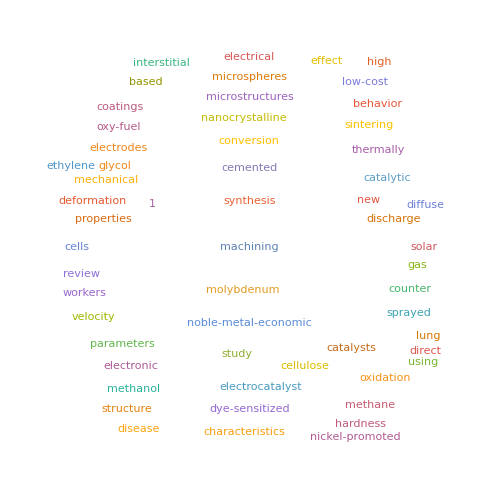

```mathematica
WordCloud@dataParsed
```

{direct->effect,direct->effect,cellulose->cells,cellulose->cells,ethylene->methane,ethylene->methane,glycol->gas,glycol->gas,using->lung,using->lung,nickel-promoted->cellulose,nickel-promoted->cemented,hardness->workers,deformation->oxidation,hardness->workers,deformation->oxidation,diffuse->disease,interstitial->sintering,lung->using,disease->diffuse,workers->direct,diffuse->disease,interstitial->sintering,lung->using,disease->diffuse,workers->direct}

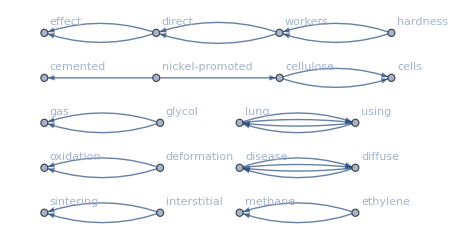

```mathematica
associate[dataParsed]
Graph[%,VertexLabels->"Name",ImageSize->450]
```

{catalytic->catalysts,catalytic->cemented,conversion->counter,conversion->synthesis,catalysts->catalytic,catalysts->synthesis,cemented->counter,cemented->catalytic,low-cost->conversion,low-cost->catalysts,molybdenum->counter,molybdenum->machining,counter->cemented,counter->conversion,synthesis->conversion,synthesis->catalysts,study->counter,study->catalytic,machining->counter,machining->catalytic}

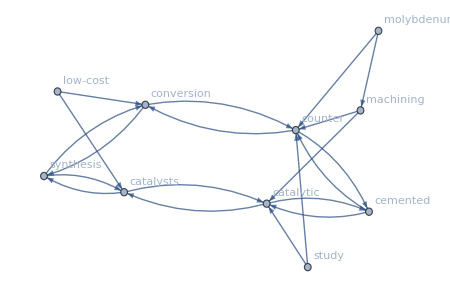

```mathematica
commonAssociateMinus[dataParsed,10,""]
Graph[%,VertexLabels->"Name",ImageSize->450]
```

{catalytic->catalysts,catalytic->cemented,conversion->counter,conversion->synthesis,catalysts->catalytic,catalysts->cells,cemented->counter,cemented->cells,low-cost->effect,low-cost->conversion,molybdenum->counter,molybdenum->solar,counter->cemented,counter->solar,electrodes->cemented,electrodes->methane,dye-sensitized->cemented,dye-sensitized->low-cost,solar->cells,solar->gas,cells->solar,cells->new,new->gas,new->cells,methane->cemented,methane->solar,synthesis->conversion,synthesis->catalysts,gas->new,gas->solar,study->solar,study->cells,effect->new,effect->cemented,machining->methane,machining->counter,parameters->catalytic,parameters->catalysts,characteristics->catalytic,characteristics->catalysts}

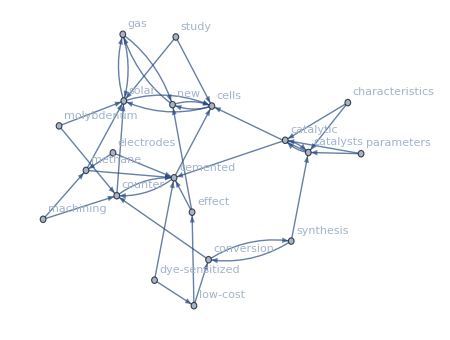

```mathematica
commonAssociateMinus[dataParsed,20,""]
Graph[%,VertexLabels->"Name",ImageSize->450]
```